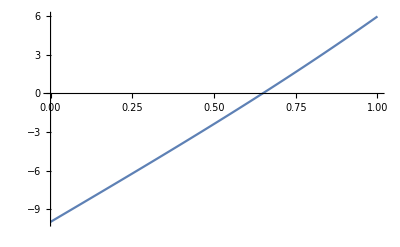

-1/15<M<0

```mathematica
f[x_]:=x^3+15x-10;
φ[x_]:=(*1/(3*x^2+15)*)x+M*f[x];
Plot[f[x],{x,0,1}]
Clear[M,x];
Reduce[0<(D[φ[x],x]/.x->0)<1,M]
```

```mathematica
M=-0.05;
xMin = 0;
xMax = 1;
h = 0.01;
xMin=0;
Clear[iter,x1,x2];
x0=0;
x1=φ[x0]
x2=φ[x1]
iter=0;
Print[(x2-x1)^2/Abs[2x1-x2-x0]];
While[(x2-x1)^2/Abs[2x1-x2-x0]≥h,
x0=x1;
x1=x2;
x2=φ[x1];
iter++;
If[iter>100,Break[]]]
Print["Метод простых итераций нашел корень x=",N[x2]," при заданной точности ε=",h,",\nпотребовавшееся количество итераций - ",iter]
Print["x=",x2];
Print["y=",f[x2]];
```

0.5

0.61875

0.0369877

Метод простых итераций нашел корень x=0.642843 при заданной точности ε=0.01,
потребовавшееся количество итераций - 1

x=0.642843

y=-0.0917015

```mathematica
mid=0;
mod=0;
While[(xMax-xMin)>h,{
mid=(xMax+xMin)/2;
If[xMin*mid>0,xMin=mid,xMax=mid];
mod=xMax-xMin;}];
Print[N[xMin]];
```

0.790533

```mathematica
xMin=0.6;
xMax=0.8;
i=0;
For[xMin=0,Abs[f[xMin]]>h,,{
(*div[x_]:=3x^2+15;*)
xMin-=f[xMin]/(D[f[z],z])/.z->xMin;
i++;}];
Print["x=",N[xMin]];
Print[f[xMin]+0.0];
Solve[f[y]==0,y]
Print["x=",N[y/.%[[3]]]];
```

x=0.648526

0.000652192

{{y→Root0.648Root[-10+15 #1+#1^3&,1]0.6484859710168895},{y→Root-0.324-3.91 ⅈRoot[-10+15 #1+#1^3&,2]-0.3242429855084443},{y→Root-0.324+3.91 ⅈRoot[-10+15 #1+#1^3&,3]-0.3242429855084443}}

x=-0.324243+3.91349 ⅈ